# 4

## PHAS2443: Practical Mathematics II Lecture 4: Time-Dependent Problems

In a great many problems in physics we are faced with fields which vary in one or more spatial dimensions and also in time, which leads us automatically into the realm of partial differential equations (PDE). We touched on time-varying problems at the end of the previous lecture, but now we shall take a more systematic look at them. Our model problem will be one of heat flow (though, as noted before, the equations will have the same form as for a diffusion problem).
  First, we need to derive the equation: for the present we shall stick to one spatial dimension. If the temperature is θ(x,t), we know from the theory of conduction that the heat flow per unit area is proportional to the temperature gradient, with the constant of proportionality being the thermal conductivity κ:
    Q(x,t) =  - κ dθ/dx.
  Now consider the heat flow associated with a slice of material between x and x+δx. For simplicity, take the cross-sectional area to be unity (you can readily check that if you choose any other area the area will cancel out in the final equation). Any imbalance in the heat flows will result in heating or cooling of the slice of material:

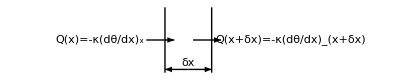

```mathematica
Show[Graphics[{Line[{{-1,-1},{-1,1}}],Line[{{1,-1},{1,1}}],Arrow[{{-1.8,0},{-0.6,0}}],Arrow[{{0.2,0},{1.4,0}}],Arrow[{{0,-0.9},{-1,-0.9}}],Arrow[{{0,-0.9},{1,-0.9}}],Text["δx",{0,-.7}],Text["Q(x)=-
StyleBox[\"κ\",\nFontSize->14]
StyleBox[\"(\",\nFontSize->24]dθ/dx
StyleBox[SubscriptBox[
  StyleBox[\")\",\nFontSize->24], \"x\"],\nFontSize->14]",{-3.8,0}],Text["Q(x+δx)=-κ
StyleBox[\"(\",\nFontSize->24]dθ/dx
StyleBox[SubscriptBox[
  StyleBox[\")\",\nFontSize->24], 
  RowBox[{\"x\", \"+\", \"δx\"}]],\nFontSize->14]",{4.4,0}]},BaseStyle->{FontFamily->"Times",FontSize->12}],PlotRange->{{-6.5,7.5},All}]
```

The net rate at which heat is deposited in the layer is
  (heat in - heat out) = Q(x) - Q(x+δx) = κ (dθ/dx)_(x+δx)-κ (dθ/dx)_x
  which will equal the heat capacity of the layer multiplied by the time rate of change of temperature. If c is the specific heat capacity and ρ the mass density of the material, we have -- using partial derivatives as we are now treating θ as a function of both x and t 
    cρ δx (∂θ)/(∂t)= κ((∂θ)/(∂x))_(x+δx)-κ ((∂θ)/(∂x))_x 
    so that
    (∂θ)/(∂t)=1/cρ (κ((∂θ)/(∂x))_(x+δx)-κ ((∂θ)/(∂x))_x)/δx= κ/cρ (∂^2 θ)/(∂ x^2).
    This, then, is our final differential equation -- first order in time and second order in space.
    
      We now discretise the problem, taking steps Δt in time and Δx in space, and label the space-time point (i Δx, n Δt) by (i,n). For the spatial derivative we use the approximation
      ((∂^2 θ)/(∂ x^2))_(i,n)≈ (θ_(i+1,n)-2 θ_(i,n)+θ_(i-1,n))/Δx^2. When it comes to the time derivative, however, we have to think a little: should we use a forward, backward, or centred scheme?

## Explicit methods

The simplest approach to the time evolution is to use a forward-difference form for the time derivative, so that
(θ_(i,n+1)-θ_(i,n))/Δt=  κ/cρ(θ_(i+1,n)-2 θ_(i,n)+θ_(i-1,n))/Δx^2
which we can rewrite as
θ_(i,n+1)= ζ (θ_(i+1,n)+θ_(i-1,n)) + (1-2ζ) θ_(i,n),
where we have written ζ for the dimensionless parameter (κ Δt)/(cρ Δx^2). We can see that the scheme is particularly simple, and that the value of the temperature at each point is given directly by the values at that point and its neighbours at the previous time step. This is called an explicit finite difference method.

  Let's implement this method for a sample problem. Consider a bar, initially at a temperature of 300 K, in which the temperature of one end is raised, at time zero, to 500 K whilst the other end is held at 300 K. Suppose the bar is 1 m long, and we discretise it into lengths Δx of 0.1 m. For a realistic metal the thermal conductivity might be κ=200 W m^-1 K^-1,  the specific heat capacity c=1000 J kg^-1 K^-1, and the density ρ=2500 kg m^-3, giving for κ/cρ (a quantity called the thermal diffusivity) a value of  8 10^-5 m^2 s^-1. Now we can see what happens as we follow through the integration with various time steps, Δt. We'll start with a time step of 50 s, and find that after 100 time steps we get the expected linear variation of temperature along the bar, and at intermediate times we can see the temperature variation evolving. As we vary the time step, say to 75, we can see that something is going badly wrong. A little experimentation shows that as soon as ζ exceeds 0.5 we have problems.

0.496

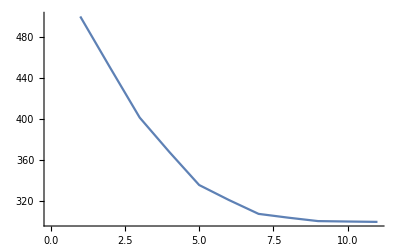

```mathematica
Δt=62;Δx=0.1;ζ=(8. Δt)/(10^5 Δx^2)
θ=Table[300,{x,0,1,Δx}];
θ⟦1⟧=500;
step[θ_]:=Module[{θp},θp=ζ (RotateRight[θ]+RotateLeft[θ])+(1-2 ζ) θ;θp⟦1⟧=500;θp⟦-1⟧=300;θp]
res=NestList[step,θ,100];
ListPlot[res⟦10⟧,Joined->True]
```

### Stability

We've seen, in practical terms, that we have problems if we take too long a time-step, that is, if the dimensionless parameter ζ=(κ Δt)/(cρ Δx^2)is too large. We can show this with a little matrix algebra. First we rewrite the finite difference equations in matrix form. If we write the list of temperatures at time-step n as a vector θ_n and collect the boundary conditions into another vector b (in principle, we could have time-dependent boundary values, but we ignore this for the moment), 
 θ_(i,n+1)= ζ (θ_(i+1,n)+θ_(i-1,n)) + (1-2ζ) θ_(i,n) becomes
  θ_(n+1)=M θ_n + b
  where the matrix M is a tridiagonal matrix -- for example, if there are 7 points in the spatial mesh 
  M=(1-2ζ | ζ | 0 | 0 | 0
ζ | 1-2ζ | ζ | 0 | 0
0 | ζ | 1-2ζ | ζ | 0
0 | 0 | ζ | 1-2ζ | ζ
0 | 0 | 0 | ζ | 1-2ζ)
  and the boundary condition vector is
  b=(ζ θ_1
0
0
0
ζ θ_7).
  Now consider what happens if the calculation is not perfect, but contains errors in the values of θ at time step n: let these errors be represented by the vector ϵ_n. These errors will propagate into the next time step:
   θ_(n+1)+ ϵ_(n+1)= M (θ_n+ ϵ_n) + b, or
   ϵ_(n+1)=M  ϵ_n.
   This equation tells us that the propagation of errors depends only on the properties of the matrix M, and not on the boundary conditions, so that if we evolve the system for s steps
   ϵ_(n+s)=M^s  ϵ_n.
   Now comes the matrix theory. For the square matrix M we can express a general vector x as a sum of the eigenvectors v_i of M:
   x=∑_(i=1)^N c_i v_i
   where N is the dimension of the matrix (two less than the number of points in the mesh) and the eigenvalue property tells us that
    M v_i= λ_i v_i.
    It follows that if we keep multiplying by M we find
     M^s x= ∑_(i=1)^N c_i λ_i^s v_i,
     which will eventually be dominated by the largest eigenvalue -- and there we see the problem: if the largest eigenvalue has a magnitude greater than one, the resulting vector will growth without limit. In our case, any error will grow without limit.
     
     The crucial question, then, is how large the eigenvalues of the propagation matrix are. They turn out to be
     λ_i=1 - 4 ζ (sin((i π)/(2(N+1))))^2,
     and it is clear that no eigenvalue can exceed 1 (as ζ is a positive quantity), but the eigenvalues are only guaranteed to be greater than -1 if 
     1-4ζ ⩾ -1, or
     ζ ⩽ 0.5.
     We have thus shown formally the condition we previously derived empirically. This condition is commonly referred to the CFL (Courant-Friedrichs–Lewy) condition for diffusion equation.

Although we have not derived the eigenvalues analytically, we can at least check them numerically.

```mathematica
trid[n_]:=Table[Which[i==j,1-2a,i==j+1,a,i==j-1,a,True,0],{i,1,n},{j,1,n}]
MatrixForm[trid[8]]
ex=Det[trid[8]-DiagonalMatrix[Table[λ,{8}]]]
ex/.λ->1-4a Sin[i π/(2(8+1))]^2//Simplify
%/.i->3//N
```

(1-2 a | a | 0 | 0 | 0 | 0 | 0 | 0
a | 1-2 a | a | 0 | 0 | 0 | 0 | 0
0 | a | 1-2 a | a | 0 | 0 | 0 | 0
0 | 0 | a | 1-2 a | a | 0 | 0 | 0
0 | 0 | 0 | a | 1-2 a | a | 0 | 0
0 | 0 | 0 | 0 | a | 1-2 a | a | 0
0 | 0 | 0 | 0 | 0 | a | 1-2 a | a
0 | 0 | 0 | 0 | 0 | 0 | a | 1-2 a)

1-16 a+105 a^2-364 a^3+715 a^4-792 a^5+462 a^6-120 a^7+9 a^8-8 λ+112 a λ-630 a^2 λ+1820 a^3 λ-2860 a^4 λ+2376 a^5 λ-924 a^6 λ+120 a^7 λ+28 λ^2-336 a λ^2+1575 a^2 λ^2-3640 a^3 λ^2+4290 a^4 λ^2-2376 a^5 λ^2+462 a^6 λ^2-56 λ^3+560 a λ^3-2100 a^2 λ^3+3640 a^3 λ^3-2860 a^4 λ^3+792 a^5 λ^3+70 λ^4-560 a λ^4+1575 a^2 λ^4-1820 a^3 λ^4+715 a^4 λ^4-56 λ^5+336 a λ^5-630 a^2 λ^5+364 a^3 λ^5+28 λ^6-112 a λ^6+105 a^2 λ^6-8 λ^7+16 a λ^7+λ^8

a^8 (1+2 Cos[(2 i π)/9]+2 Cos[(4 i π)/9]+2 Cos[(2 i π)/3]+2 Cos[(8 i π)/9])

0.

### Consistency

Really we should have dealt with consistency and stability in the opposite order, but as our numerical experiments showed us the stability problem we looked at that first. Consistency addresses a slightly different question, namely, whether as the time and space intervals both tend to zero we really recover the differential equation. 

First, we take an informal approach to the problem. Consider the explicit scheme for the diffusion equation,
 θ_(i,n+1)= ζ (θ_(i+1,n)+θ_(i-1,n)) + (1-2ζ) θ_(i,n),
 and replace the values of θ evaluated other than at position i Δx, time n Δt, by their Taylor expansions about i,n:
 θ_(i,n+1)=θ_(i,n)+ Δt (∂θ_(i,n))/(∂t)+1/2 Δt^2(∂^2 θ_(i,n))/(∂t^2)+...
 θ_(i+1,n)=θ_(i,n)+ Δx (∂θ_(i,n))/(∂x)+1/2 Δx^2(∂^2 θ_(i,n))/(∂x^2)+1/(3!)Δx^3(∂^3 θ_(i,n))/(∂x^3)+...
 θ_(i-1,n)=θ_(i,n)- Δx (∂θ_(i,n))/(∂x)+1/2 Δx^2(∂^2 θ_(i,n))/(∂x^2)-1/(3!)Δx^3(∂^3 θ_(i,n))/(∂x^3)+...
 so that we obtain
θ_(i,n)+ Δt (∂θ_(i,n))/(∂t)+1/2 Δt^2(∂^2 θ_(i,n))/(∂t^2)+...= ζ (θ_(i,n)+ Δx (∂θ_(i,n))/(∂x)+1/2 Δx^2(∂^2 θ_(i,n))/(∂x^2)+1/(3!)Δx^3(∂^3 θ_(i,n))/(∂x^3)+...+θ_(i,n)- Δx (∂θ_(i,n))/(∂x)+1/2 Δx^2(∂^2 θ_(i,n))/(∂x^2)-1/(3!)Δx^3(∂^3 θ_(i,n))/(∂x^3)+...) + (1-2ζ) θ_(i,n).
Rearranging,
 Δt (∂θ_(i,n))/(∂t)+1/2 Δt^2(∂^2 θ_(i,n))/(∂t^2)+...= ζ (Δx^2(∂^2 θ_(i,n))/(∂x^2)+2/(4!)Δx^4(∂^4 θ_(i,n))/(∂x^4)+...) 
or (recalling that ζ=(κ Δt)/(cρ Δx^2))
  (∂θ_(i,n))/(∂t)-κ/cρ(∂^2 θ_(i,n))/(∂x^2)=  (2ζ)/(4!)Δx^2(∂^4 θ_(i,n))/(∂x^4)-1/2 Δt(∂^2 θ_(i,n))/(∂t^2)...
=2/(4!)κ/cρ Δt(∂^4 θ_(i,n))/(∂x^4)-1/2 Δt(∂^2 θ_(i,n))/(∂t^2)...
 and we can see that as Δt tends to zero the right-hand side tends to zero, and we recover
   (∂θ_(i,n))/(∂t)-κ/cρ(∂^2 θ_(i,n))/(∂x^2)=0,
 the original differential equation.
 
We can go through this more formally, by considering the way in which the finite difference solution converges on the exact solution. In this case we need to add one more mathematical trick to our armoury. This is the fact that for any single-valued function f(x) which is continuous in the range x_1⩽x⩽x_2 it is possible to write
  f(x_3) = 1/2(f(x_1)+f(x_2)) 
  where x_1⩽x_3⩽x_2. The best way of convincing oneself of the truth of this is probably by drawing a graph.
  
    Now suppose that in solving the diffusion equation using the explicit method,
     θ_(i,n+1)= ζ (θ_(i+1,n)+θ_(i-1,n)) + (1-2ζ) θ_(i,n),
     the values θ found in the numerical simulation differ slightly from the exact values, Θ. Write the error term as
     ϵ_(i,n)=θ_(i,n)-Θ_(i,n).
     Substituting, then, we find
     ϵ_(i,n+1)= ζ (ϵ_(i+1,n)+ϵ_(i-1,n)) + (1-2ζ) ϵ_(i,n)+ζ (Θ_(i+1,n)+Θ_(i-1,n)) + (1-2ζ) Θ_(i,n)-Θ_(i,n+1). 
     Now use the Taylor expansion, but keep the correct remainder term (remember that this involved the properties of the function at a point somewhere within the expansion interval -- you can see where this is going). So, for example,
       Θ_(i+1,n)= Θ_(i,n)+Δx(∂Θ_(i,n))/(∂x) +(Δx)^2/2 ((∂^2 Θ)/(∂x^2))_(x=x̄,n),
       where i Δx⩽x̄⩽ (i+1)Δx.
       We can do the same thing for the expansion towards (i-1)Δx and for the expansion in time, and put the results together, to find
       ϵ_(i,n+1)= ζ (ϵ_(i+1,n)+ϵ_(i-1,n)) + (1-2ζ) ϵ_(i,n)-Δt [((∂Θ)/(∂t))_(i,t=t̄)-κ/(2cρ){ ((∂^2 Θ)/(∂x^2))_(x=x̄,n)+ ((∂^2 Θ)/(∂x^2))_(x=OverBar[x'],n)}],
       where x̄ and OverBar[x'] represent the error terms in the forward and backward differences in space. Now at any time step, n, there will be different error terms for different space points i. As long as we insist that (1-2ζ) is positive or zero, though, we can work in terms of the maximum error at any step, E_n, and if we write the quantity in square brackets as Q we have
       |ϵ_(i,n+1)| ⩽ ζ(E_n+E_n) + (1-2ζ) E_n + Q Δt
= E_n + Q Δt.
       So we can see that as the time-step Δt tends to zero the growth in the error also tends to zero -- but as the error in the initial condition is assumed to be zero this means that the error tends to zero. Furthermore, as both Δx and Δt tend to zero the term in square brackets tends to the differential equation
       [(∂Θ)/(∂t)-κ/cρ(∂^2 Θ)/(∂x^2)]
   with all the terms evaluated at the same x and t, which we know is zero. 
       
        We have proved that the difference equation we have derived can be made consistent. The condition for consistency is rather boring, as it is the same as the stability condition, but this is not always the case. The exercises accompanying this lecture explore a more interesting case.

### Symplectic Integration

If we think of a particle moving in one dimension, we can plot a two-dimensional curve representing its velocity and position as a function of time: a plot with velocity on one axis and position on another is called a phase plot. Now the velocity determined the kinetic energy, and the position determines the potential energy, so each point in phase space has a particular energy. Furthermore, a particle with fixed energy must stay on a constant energy surface. Symplectic integrators are designed to keep the deviation of a particle's trajectory in phase space within a small distance of the appropriate constant energy surface. Actually, the concept is rather more general than that, and other conserved quantities (momentum, angular momentum,...) may be specified, but that is the gist of it. In the exercises we will explore the dynamics of particles, and show experimentally the superiority of a particular family of algorithms (the Verlet algorithms) which can be shown to be symplectic to various orders in the time-step.

## Implicit Methods

What we have done up to now is to treat (θ_(i,n+1)-θ_(i,n))/Δt as a one-sided finite difference approximation to the time derivative at (i,n). We could, however, think of it as a centred difference approximation to the time derivative at (i,n+1/2). As we know that the centred difference is accurate to higher order than the one-sided difference, we might hope to get a better difference scheme if we can use this idea. That means we need the spatial derivative at the half-time-step too. We will take
((∂^2 θ)/(∂ x^2))_(i,n+1/2)=1/2 [((∂^2 θ)/(∂ x^2))_(i,n)+((∂^2 θ)/(∂ x^2))_(i,n+1)],
with
((∂^2 θ)/(∂ x^2))_(i,n)≈ (θ_(i+1,n)-2 θ_(i,n)+θ_(i-1,n))/Δx^2 
and
((∂^2 θ)/(∂ x^2))_(i,n+1)≈ (θ_(i+1,n+1)-2 θ_(i,n+1)+θ_(i-1,n+1))/Δx^2.
Inserting these approximations in the differential equation gives
(θ_(i,n+1)-θ_(i,n))/Δt=κ/(2cρ)[(θ_(i+1,n)-2 θ_(i,n)+θ_(i-1,n))/Δx^2+(θ_(i+1,n+1)-2 θ_(i,n+1)+θ_(i-1,n+1))/Δx^2],
which can be rearranged as
-ζ θ_(i-1,n+1)+ 2(1+ζ) θ_(i,n+1) - ζ θ_(i+1,n+1) = ζ θ_(i-1,n) + 2(1-ζ) θ_(i,n) + ζ θ_(i+1,n),
with ζ defined in the same way as before, as ζ=(κ Δt)/(cρ Δx^2).
  The only problem with this equation is that it does not give the temperature at one point at one timestep explicitly in terms of the values at the point and its neighbours at the previous step -- it gives a set of equations that must be solved to find the new temperatures. This is called an implicit finite difference scheme: more precisely, this is the Crank-Nicholson implicit method. Solving the equations is not a problem for us, though, as these linear equations have just the same tridiagonal form as the one we solved with the two-point boundary steady-state heat flow problem in Lecture 3.
  
    We can rewrite the equation in a matrix form, as
    M θ_(n+1) = c_n,
    where, for our 7-spatial-element problem,
    M = (2(1+ζ) | -ζ | 0 | 0 | 0
-ζ | 2(1+ζ) | -ζ | 0 | 0
0 | -ζ | 2(1+ζ) | -ζ | 0
0 | 0 | -ζ | 2(1+ζ) | -ζ
0 | 0 | 0 | -ζ | 2(1+ζ))
    and the right-hand side must incorporate both the temperature at the previous step and the boundary conditions. For the effect of the previous step it is convenient again to adopt a matrix form, so that the set of terms
    c_n = ζ θ_(i-1,n) + 2(1-ζ) θ_(i,n) + ζ θ_(i+1,n)
can be written as
   (2(1-ζ) | ζ | 0 | 0 | 0
ζ | 2(1-ζ) | ζ | 0 | 0
0 | ζ | 2(1-ζ) | ζ | 0
0 | 0 | ζ | 2(1-ζ) | ζ
0 | 0 | 0 | ζ | 2(1-ζ))(θ_(2,n)
θ_(3,n)
θ_(4,n)
θ_(5,n)
θ_(6,n)),
   or
    N θ_n .
    So the equations become
     (2(1+ζ) | -ζ | 0 | 0 | 0
-ζ | 2(1+ζ) | -ζ | 0 | 0
0 | -ζ | 2(1+ζ) | -ζ | 0
0 | 0 | -ζ | 2(1+ζ) | -ζ
0 | 0 | 0 | -ζ | 2(1+ζ))(θ_(2,n+1)
θ_(3,n+1)
θ_(4,n+1)
θ_(5,n+1)
θ_(6,n+1))=(2ζ θ_1
0
0
0
2ζ θ_7)+ (2(1-ζ) | ζ | 0 | 0 | 0
ζ | 2(1-ζ) | ζ | 0 | 0
0 | ζ | 2(1-ζ) | ζ | 0
0 | 0 | ζ | 2(1-ζ) | ζ
0 | 0 | 0 | ζ | 2(1-ζ))(θ_(2,n)
θ_(3,n)
θ_(4,n)
θ_(5,n)
θ_(6,n)).
     (the factor of 2 in the first vector on the right-hand side comes from the fact that there is a term ζ θ_(1,n+1) and a term ζ θ_(1,n).
     If we write the boundary condition vector as b, we have
     M θ_(n+1) = b_n + N θ_n ,
     with the solution
    θ_(n+1) =  M^-1  b_n +  M^-1N θ_n .
     Although this looks as if it is going to involve a lot more computation, we only have to calculate the matrices  M^-1  and  M^-1N  once at the beginning of the problem, as they do not change thereafter (assuming that the material properties do not change with temperature and we keep the time-step constant so that ζ is constant).

Now that we have the theory in place, we'll set the problem up in Mathematica code and compare it with the explicit time-stepping method. We tackle the same problem as before. We will see that it is possible to take much longer time-steps than before (try 50, 75, 100). If the step is made very long (500 or 1000, say), some noise will appear in the solution but the general trend will still be correct.

0.4

11

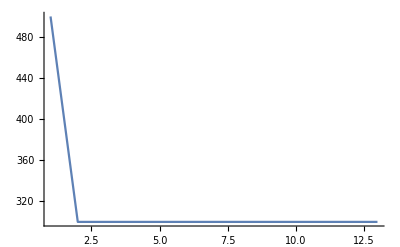

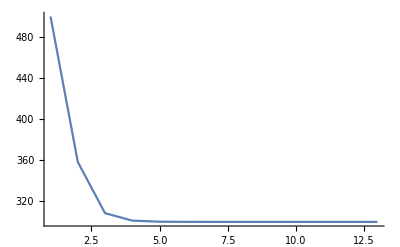

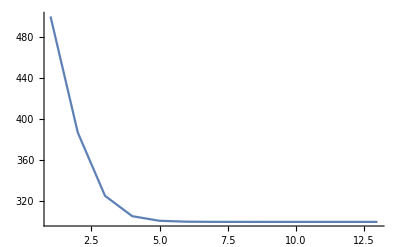

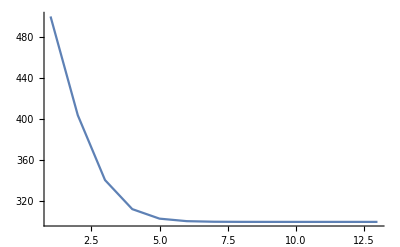

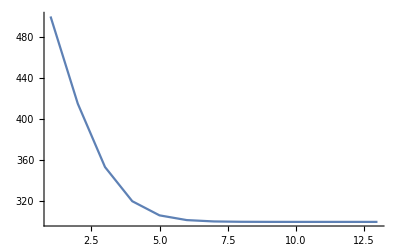

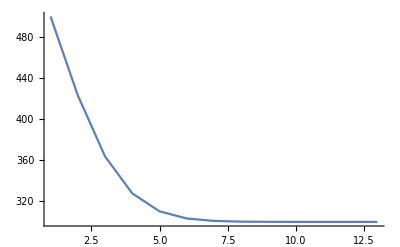

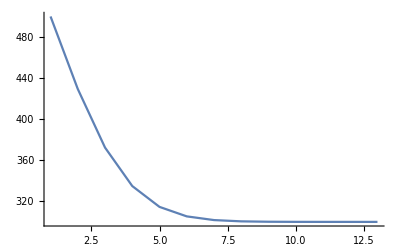

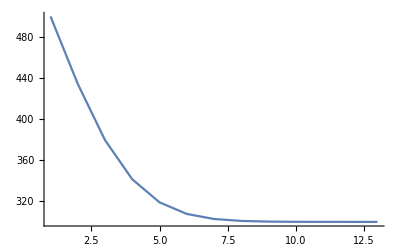

```mathematica
Δt=50;Δx=0.1;ζ=(8. Δt)/(10^5 Δx^2)
bcl=500;bcr=300;
nx=Floor[1./Δx]+1
θ=Table[300,{i,1,nx}];
bvec=2 ζ Append[Prepend[Table[0,{i,2,nx-1}],bcl],bcr];
mmat=Table[Which[i==j,2 (1+ζ),i==j+1,-ζ,i==j-1,-ζ,True,0],{i,1,nx},{j,1,nx}];
nmat=Table[Which[i==j,2 (1-ζ),i==j+1,ζ,i==j-1,ζ,True,0],{i,1,nx},{j,1,nx}];
mmatinv=MatrixPower[mmat,-1];
mmatinvnmat=mmatinv.nmat;
mmatinvbvec=mmatinv.bvec;
step[θ_List]:=mmatinvbvec+mmatinvnmat.θ
res=NestList[step,θ,100];
Do[Print[ListPlot[Append[Prepend[res⟦i⟧,bcl],bcr],Joined->True,PlotRange->All]],{i,1,10}]
```

Although we shall not do so here, we can use the same approaches as for the explicit method to study the consistency and stability of this Crank-Nicholson method. We find that not only is the method consistent, it is also stable for all values of ζ. Thus it is possible to show formally what we have discovered empirically.

## Summary

Explicit finite difference schemes become unstable if one takes too long a time-step. This is more than just the loss of accuracy one expects because the finite difference approximation becomes a less good approximation to the derivative -- the unstable scheme actually generates nonsense. An implicit scheme often extends the range of stability, sometimes indefinitely.

A.H. Harker
Physics and Astronomy, UCL
September 2005, revised January 2009
Amended by Patrick Guio, Physics and Astronomy, UCL, February 2015-2017